# CCBH: direct method

L . Amendola 2023; produces some of the exclusion plots of paper XXX

```mathematica
SetDirectory[NotebookDirectory[]]

figdir="figures/";

(* m1 data *)
fulldata={{0.0900.0300.030,35.63.15.},{0.210.090.09,23.6.15.},{0.090.040.04,13.73.29.},{0.200.080.08,31.6.7.},{0.0700.0200.020,11.01.76.},{0.490.210.19,50.10.16.},{0.200.070.05,35.6.8.},{0.1200.040.030,30.63.06.},{0.210.070.07,35.5.8.},{0.350.150.15,40.7.11.},{0.290.110.07,24.83.55.},{0.150.040.04,28.6.6.},{0.620.260.32,51.13.17.},{0.450.190.21,42.7.10.},{0.290.100.10,41.8.10.},{0.280.100.08,23.6.6.},{0.400.130.14,36.10.11.},{0.330.150.26,39.9.14.},{0.450.150.24,65.11.11.},{0.560.270.4,98.22.34.},{0.210.100.10,43.6.6.},{0.440.190.29,36.8.19.},{0.490.200.26,72.15.18.},{0.500.200.23,58.13.19.},{0.180.070.09,35.6.7.},{0.380.120.11,54.8.13.},{0.600.290.33,74.17.20.},{0.170.080.06,12.12.02.6},{0.190.070.06,20.4.4.},{0.160.050.11,14.23.36.},{0.520.180.18,39.6.9.},{0.180.070.05,12.52.37.},{0.540.220.22,38.7.10.},{0.0500.0100.010,23.31.41.4},{0.380.150.10,32.4.5.},{0.290.110.11,24.7.7.},{0.290.110.17,44.7.8.},{0.320.110.11,33.5.9.},{0.110.040.04,8.81.84.},{0.190.070.08,20.82.97.},{0.530.200.33,66.17.22.},{0.160.060.06,14.4.8.},{0.230.090.07,10.71.64.},{0.250.120.18,65.11.11.},{0.570.290.4,53.20.47.},{0.160.060.05,10.72.14.},{0.130.050.04,11.91.83.3},{0.350.140.13,25.4.7.},{0.0700.0300.020,12.12.35.},{0.510.260.23,45.8.11.},{0.690.270.26,49.10.14.},{0.240.080.07,36.5.7.},{0.0600.0200.030,5.92.52.0},{0.560.280.28,42.8.12.},{0.180.070.05,34.53.210.},{0.0900.0300.030,10.11.43.5},{0.400.140.15,38.6.9.},{0.570.260.25,36.7.11.},{0.570.220.22,38.7.10.},{0.320.110.08,40.5.7.},{0.220.100.09,19.33.05.},{0.280.120.16,38.9.9.},{0.230.070.05,34.4.6.},{0.220.080.08,13.12.910.},{0.560.210.25,34.6.10.},{0.610.300.4,37.11.42.},{0.200.080.09,11.83.010.},{0.560.260.31,42.9.13.},{0.90.40.4,46.11.15.},{0.150.060.05,9.74.3.4},{0.200.090.09,11.82.26.},{0.630.290.4,51.13.22.}};
data={{0.09,35.6},{0.21,23.2},{0.09,13.7},{0.2,30.8},{0.07,11.},{0.49,50.2},{0.2,35.},{0.12,30.6},{0.21,35.4},{0.35,39.5},{0.29,24.8},{0.15,27.7},{0.62,51.3},{0.45,42.},{0.29,41.3},{0.28,23.2},{0.4,36.},{0.33,39.2},{0.45,65.1},{0.56,98.4},{0.21,43.4},{0.44,35.6},{0.49,71.8},{0.5,58.},{0.18,35.1},{0.38,54.1},{0.6,74.},{0.17,12.1},{0.19,19.8},{0.16,14.2},{0.52,38.9},{0.18,12.5},{0.54,37.7},{0.05,23.3},{0.38,31.9},{0.29,23.7},{0.29,43.8},{0.32,32.6},{0.11,8.8},{0.19,20.8},{0.53,66.3},{0.16,14.2},{0.23,10.7},{0.25,65.},{0.57,53.},{0.16,10.7},{0.13,11.9},{0.35,24.9},{0.07,12.1},{0.51,45.1},{0.69,49.4},{0.24,35.6},{0.06,5.9},{0.56,42.2},{0.18,34.5},{0.09,10.1},{0.4,37.8},{0.57,35.6},{0.57,37.5},{0.32,40.},{0.22,19.3},{0.28,37.8},{0.23,34.2},{0.22,13.1},{0.56,33.7},{0.61,36.6},{0.2,11.8},{0.56,41.8},{0.92,46.2},{0.15,9.7},{0.2,11.8},{0.63,51.}};
(* m2 data *)
datam2={{0.09,30.6},{0.21,13.6},{0.09,7.7},{0.2,20.},{0.07,7.6},{0.49,34.},{0.2,23.8},{0.12,25.2},{0.21,26.7},{0.35,29.},{0.29,18.5},{0.15,9.},{0.62,30.4},{0.45,32.},{0.29,28.3},{0.28,12.5},{0.4,18.3},{0.33,24.},{0.45,40.8},{0.56,57.2},{0.21,33.4},{0.44,22.2},{0.49,44.8},{0.5,35.},{0.18,24.},{0.38,40.5},{0.6,39.4},{0.17,7.9},{0.19,11.6},{0.16,7.5},{0.52,30.2},{0.18,8.},{0.54,27.6},{0.05,2.6},{0.38,25.8},{0.29,10.4},{0.29,34.2},{0.32,24.5},{0.11,5.1},{0.19,15.5},{0.53,26.8},{0.16,6.9},{0.23,7.7},{0.25,47.},{0.57,24.},{0.16,6.7},{0.13,8.2},{0.35,18.1},{0.07,7.7},{0.51,34.7},{0.69,37.},{0.24,28.3},{0.56,32.6},{0.18,28.9},{0.09,7.3},{0.4,27.4},{0.57,27.1},{0.57,27.9},{0.32,32.5},{0.22,14.},{0.28,20.},{0.23,27.7},{0.22,7.8},{0.56,24.2},{0.61,19.9},{0.2,6.3},{0.56,29.},{0.92,30.6},{0.2,7.9},{0.63,30.}};
(* m2data cutting out 2.1 and 2.6 masses *)
datam2c={{0.09,30.6},{0.21,13.6},{0.09,7.7},{0.2,20.},{0.07,7.6},{0.49,34.},{0.2,23.8},{0.12,25.2},{0.21,26.7},{0.35,29.},{0.29,18.5},{0.15,9.},{0.62,30.4},{0.45,32.},{0.29,28.3},{0.28,12.5},{0.4,18.3},{0.33,24.},{0.45,40.8},{0.56,57.2},{0.21,33.4},{0.44,22.2},{0.49,44.8},{0.5,35.},{0.18,24.},{0.38,40.5},{0.6,39.4},{0.17,7.9},{0.19,11.6},{0.16,7.5},{0.52,30.2},{0.18,8.},{0.54,27.6},{0.38,25.8},{0.29,10.4},{0.29,34.2},{0.32,24.5},{0.11,5.1},{0.19,15.5},{0.53,26.8},{0.16,6.9},{0.23,7.7},{0.25,47.},{0.57,24.},{0.16,6.7},{0.13,8.2},{0.35,18.1},{0.07,7.7},{0.51,34.7},{0.69,37.},{0.24,28.3},{0.56,32.6},{0.18,28.9},{0.09,7.3},{0.4,27.4},{0.57,27.1},{0.57,27.9},{0.32,32.5},{0.22,14.},{0.28,20.},{0.23,27.7},{0.22,7.8},{0.56,24.2},{0.61,19.9},{0.2,6.3},{0.56,29.},{0.92,30.6},{0.2,7.9},{0.63,30.}};


dt0ref=50;
tdcutref=13; (* in Gyr *)
tminref=50; (* in Myr *)
tmaxref=13;
zmaxref=10;
om=0.32;h0=1/(9.78/0.7);
wref=-1;
betaref=1;
kref=3;

variables={"zmax","k","tmin","tmax"};
varlab={"z_max","k","t_(d, min)","t_(d, max)"};
variables={"k","tmax","zmax","tmin"};
varlab={"k","t_max (Gyr)","z_max","t_min(Myr)"};
ncoord=Length[variables];
cp=Table[0,{i,ncoord},{j,ncoord}];
wrange=Table[w,{w,-.6,-1,-.05}];

krange=Table[k,{k,0.25,3,.25}];
zmaxrange=Table[zmax,{zmax,3,10,.5}];
tminrange=Table[tmin,{tmin,5,50,5}];
tmaxrange=Table[tmax,{tmax,3,13,1}];
betarange=Table[beta,{beta,1.01,1.51,.1}];

ran[xc_]:=Which[xc=="w",wrange,xc=="k",krange,xc=="tmax",tmaxrange,xc=="tmin",tminrange,xc=="zmax",zmaxrange]



sigma[x0_]:=1-NIntegrate[Exp[-1/2*x^2]/Sqrt[2*Pi],{x,-x0,x0}];

(* from https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately*)

Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->1],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

/Users/luca/Dropbox/active-project-CosmologicallyCoupledBHs/math

## Corner plot GBH

```mathematica
Clear[td];

hub[z_,w_]=h0*(om*(1+z)^3+(1-om)*(1+z)^(3*(1+w)))^(1/2); (* time is measured in Gyr *)

tdint[zi_,zm_,w_]:=NIntegrate[1/((1+z)*hub[z,w]),{z,zm,zi}]
td=Interpolation[Flatten[Table[{zi,zm,w,tdint[zi,zm,w]},{zi,0,15,.5},{zm,0,1,.1},{w,-1.5,-.5,.1}],2]];
Clear[age];age=Interpolation[Flatten[Table[{zm,w,NIntegrate[1/((1+z)*hub[z,w]),{z,0,zm}]},{zm,0,1.5,.01},{w,-1.5,-.5,.05}],1]]

agemax=Interpolation[Flatten[Table[{w,zmax,NIntegrate[1/((1+z)*hub[z,w]),{z,0,zmax}]},{w,-1.5,-.5,.05},{zmax,3,15,1}],1]];

Clear[zmin];zmin[zm_,mm_,mmin_,k_,zmax_]=Min[(1+zm)*(mmin/mm)^(-1/k)-1,zmax]
psi[dt_]=1/dt;norm=Integrate[psi[dt],{dt,dt0,dtcut},Assumptions->{dt>0 &&dt0>0 && dtcut>0 && dtcut>dt0}]
Clear[tdmin];tdmin[zm_,mm_,mmin_,k_,zmax_]=td[zmin[zm,mm,mmin,k,zmax],zm,wref];
tdistr[dt0_,tdb_,dtcut_]=Integrate[psi[dt],{dt,dt0,tdb},GenerateConditions->False]/norm;

Clear[p,fullp];p[dt0_,dtcut_,zm_,mm_,mmin_,k_,zmax_]=tdistr[dt0,If[tdmin[zm,mm,mmin,k,zmax]<Min[dtcut,agemax[wref,zmax]]-age[zm,wref],tdmin[zm,mm,mmin,k,zmax],Min[dtcut,agemax[wref,zmax]]-age[zm,wref]],Min[dtcut,agemax[wref,zmax]]-age[zm,wref]];
(* beta is added just to homogenize with previous definitions *)
fullp[dt0_,dtcut_,mmin_,k_,zmax_,beta_]:=Product[p[dt0*10^(-3),dtcut,data[[i,1]],data[[i,2]],mmin,k,zmax],{i,Length[data]}]
```

InterpolatingFunction[…]

Min[-1+(mmin/mm)^(-1/k) (1+zm),zmax]

Log[dtcut/dt0]

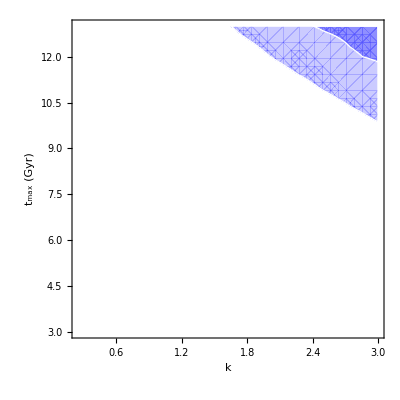

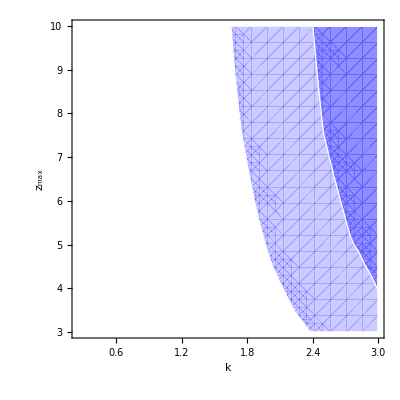

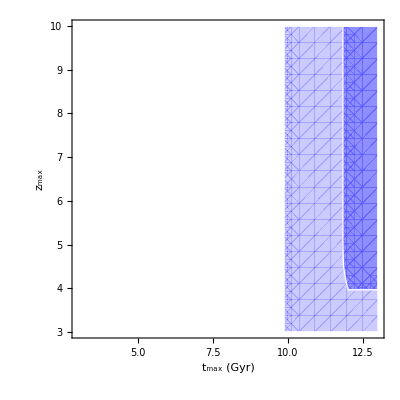

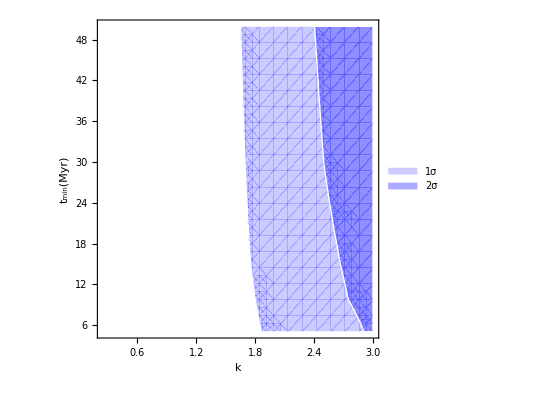

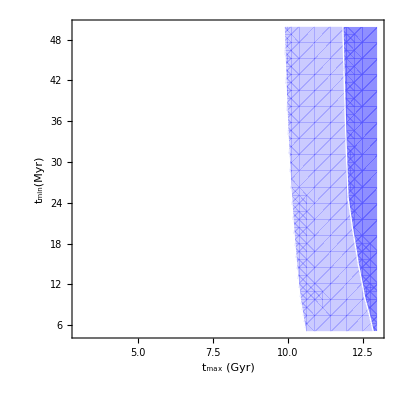

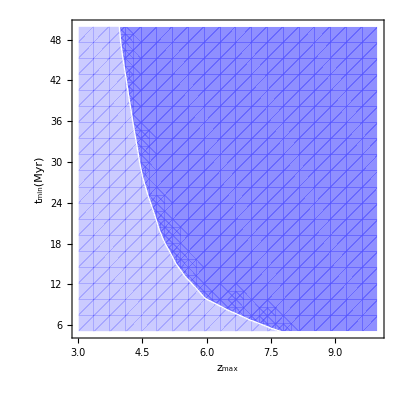

```mathematica
cp=Table[0,{i,ncoord},{j,ncoord}];



{yc="tmax",xc="k"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];ptab=Flatten[Table[{x,y,Chop[fullp[dt0ref,y,2,x,zmaxref,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}},FrameLabel->{varlab[[xcp]],varlab[[ycp]]}
]


{xc="k",yc="zmax"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[dt0ref,tmaxref,2,x,y,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]

{xc="tmax",yc="zmax"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[dt0ref,x,2,kref,y,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]

{xc="k",yc="tmin"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[y,tmaxref,2,x,zmaxref,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}},  PlotLegends -> Placed[{
    Style["1σ", FontFamily->"Times", FontSize -> 12], 
    Style["2σ", FontFamily->"Times", FontSize -> 12], 
    Style["3σ", FontFamily->"Times", FontSize -> 12],
    Style["1σ, t_min=5 Myr", FontFamily->"Times", FontSize -> 12],
    Style["2σ, t_min=5 Myr", FontFamily->"Times", FontSize -> 12]}, 
    {0.18, 0.15}
  ]
]

{xc="tmax",yc="tmin"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[y,x,2,kref,zmaxref,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]


{xc="zmax",yc="tmin"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[y,tmaxref,2,kref,x,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]
```

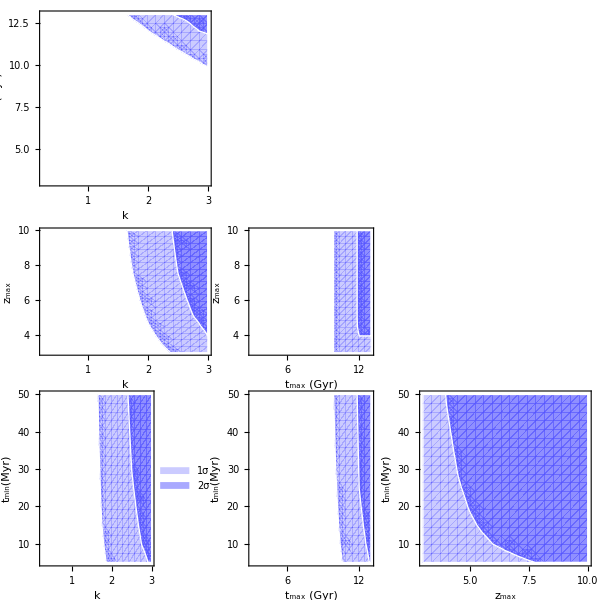

figures/GBH-corner-plot.jpg

```mathematica
cpgbh=cp;

pattern={{1,0,0},{2,4,0},{3,5,6}};pattern//TableForm;


cdp=Drop[Transpose[cp],{1},{4}];cdp//TableForm;
m=0;plot0=plot0=Show[Graphics[{{FaceForm[{Green,Opacity[0]}],EdgeForm[{Green,Opacity[0]}],Disk[]}},Frame->False,AspectRatio->1]];grid=Table[If[pattern[[i,j]]>0,cdp[[i,j]],plot0],{i,ncoord-1},{j,ncoord-1}];

Clear[pgrid];
pgrid=plotGrid[grid,600,600,ImagePadding->60]
Export[figdir<>"GBH-corner-plot.jpg",pgrid]
```

## Corner plot DEBH

```mathematica
hub[z_,w_]=h0*(om*(1+z)^3+(1-om)*(1+z)^(3*(1+w)))^(1/2); (* time is measured in Gyr *)
tdint[zi_,zm_,w_]:=NIntegrate[1/((1+z)*hub[z,w]),{z,zm,zi}]

Clear[td];
td=Interpolation[Flatten[Table[{zi,zm,w,tdint[zi,zm,w]},{zi,0,15,.5},{zm,0,1,.1},{w,-1.5,-.5,.1}],2]];
Clear[age];age=Interpolation[Flatten[Table[{zm,w,NIntegrate[1/((1+z)*hub[z,w]),{z,0,zm}]},{zm,0,1,.01},{w,-1.5,-.5,.05}],1]];
agemax=Interpolation[Flatten[Table[{w,zmax,NIntegrate[1/((1+z)*hub[z,w]),{z,0,zmax}]},{w,-1.5,-.5,.05},{zmax,3,15,1}],1]];
Clear[zmin,psi,norm,psiint];zmin[zm_,mm_,mmin_,w_,zmax_]=Min[(1+zm)*(mmin/mm)^(1/3/w)-1,zmax];
psi[dt_,beta_]=1/dt^beta;psiint[dt0_,tdb_,beta_]=If[beta!=1,((dt0 tdb)^-beta (-dt0^beta tdb+dt0 tdb^beta))/(-1+beta),Log[tdb/dt0]];
norm[dt0_,dtcut_,beta_]=If[beta!=1,psiint[dt0,dtcut,beta],psiint[dt0,dtcut,1]];
Clear[tdmin];tdmin[zm_,mm_,mmin_,w_,zmax_]:=td[zmin[zm,mm,mmin,w,zmax],zm,w]
tdistrnn[dt0_,tdb_,dtcut_,beta_]=If[beta!=1,psiint[dt0,tdb,beta],psiint[dt0,tdb,1]];
tdistr[dt0_,tdb_,dtcut_,beta_]=If[beta!=1,psiint[dt0,tdb,beta],psiint[dt0,tdb,1]]/norm[dt0,dtcut,beta];


Clear[p,fullp];pnn[dt0_,dtcut_,zm_,mm_,mmin_,w_,zmax_,beta_]:=tdistrnn[dt0,If[tdmin[zm,mm,mmin,w,zmax]<Min[dtcut,agemax[w,zmax]]-age[zm,w],tdmin[zm,mm,mmin,w,zmax],Min[dtcut,agemax[w,zmax]]-age[zm,w]],Min[dtcut,agemax[w,zmax]]-age[zm,w],beta];

p[dt0_,dtcut_,zm_,mm_,mmin_,w_,zmax_,beta_]:=tdistr[dt0,If[tdmin[zm,mm,mmin,w,zmax]<Min[dtcut,agemax[w,zmax]]-age[zm,w],tdmin[zm,mm,mmin,w,zmax],Min[dtcut,agemax[w,zmax]]-age[zm,w]],Min[dtcut,agemax[w,zmax]]-age[zm,w],beta];

fullp[dt0_,dtcut_,mmin_,w_,zmax_,beta_]:=Product[p[dt0*10^(-3),dtcut,data[[i,1]],data[[i,2]],mmin,w,zmax,beta],{i,Length[data]}];

Timing[fullp[dt0ref,tdcutref,2,-1,10,betaref]]
sigma[2.6]
```

{0.00413,0.00833879}

0.00932238

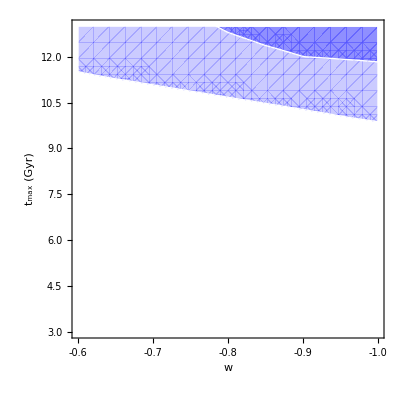

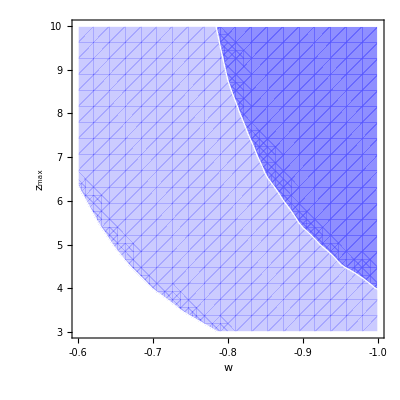

-Graphics-

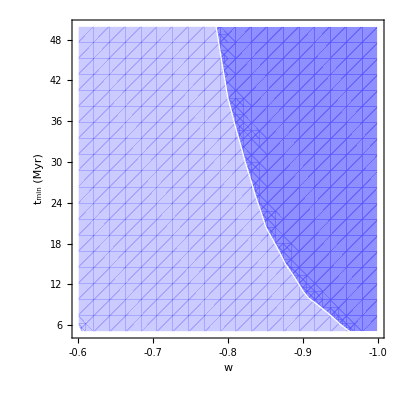

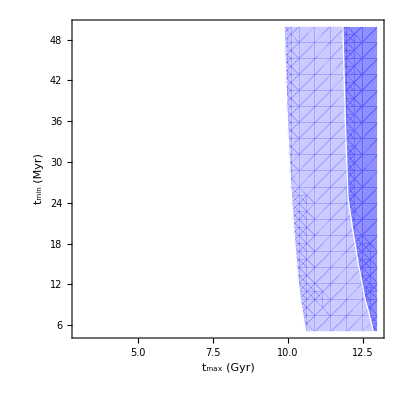

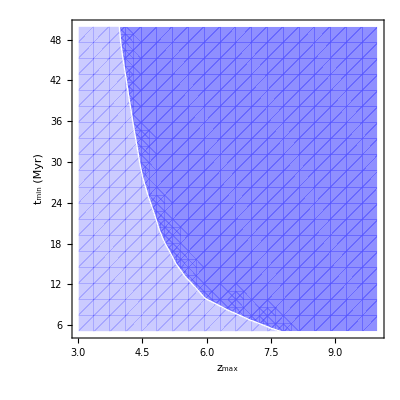

```mathematica
variables={"w","tmax","zmax","tmin"};
varlab={"w","t_max (Gyr)","z_max","t_min (Myr)"};
ncoord=Length[variables];
cp=Table[0,{i,ncoord},{j,ncoord}];



{yc="tmax",xc="w"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];ptab=Flatten[Table[{x,y,Chop[fullp[dt0ref,y,2,x,zmaxref,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}},FrameLabel->{varlab[[xcp]],varlab[[ycp]]},ScalingFunctions->{"Reverse",Identity}
]



{xc="w",yc="zmax"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[dt0ref,tmaxref,2,x,y,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}},ScalingFunctions->{"Reverse",Identity}
]

{xc="tmax",yc="zmax"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[dt0ref,x,2,wref,y,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]

{xc="w",yc="tmin"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[y,tmaxref,2,x,zmaxref,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}},ScalingFunctions->{"Reverse",Identity}
]

{xc="tmax",yc="tmin"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[y,x,2,wref,zmaxref,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]

{xc="zmax",yc="tmin"};
xrange=ran[xc];yrange=ran[yc];
labs=ToString[xc]<>"-"<>ToString[yc];
(* tmin,tmax,minmass,w,zmax,beta*)ptab=Flatten[Table[{x,y,Chop[fullp[y,tmaxref,2,wref,x,betaref]]},{y,yrange},{x,xrange}],1];
fullptab=Interpolation[ptab,InterpolationOrder->1];
xcp=Position[variables,xc][[1,1]];
ycp=Position[variables,yc][[1,1]];

cp[[xcp,ycp]]=RegionPlot[
  {
    fullptab[x,y] < sigma[1],
    fullptab[x,y]< sigma[2],
    fullptab[x,y] < sigma[3]
  },
  {x,xrange[[1]],xrange[[-1]]},{y,yrange[[1]],yrange[[-1]]},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]], None, None},
  BoundaryStyle->{1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin], 4 -> Directive[Black, Dashed], 5 -> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
 FrameLabel->{varlab[[xcp]],varlab[[ycp]]},
  PlotRange->{{xrange[[1]],xrange[[-1]]}, {yrange[[1]],yrange[[-1]]}}
]
```

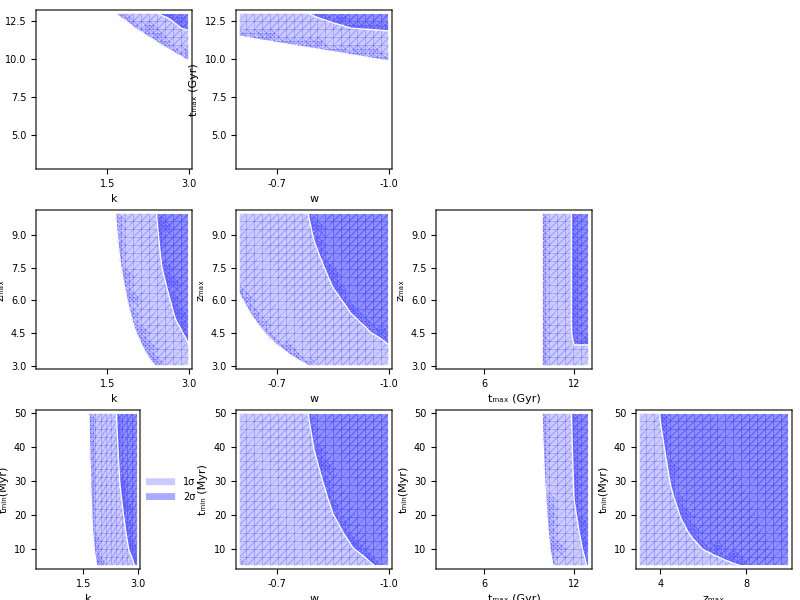

figures/full-corner-plot.jpg

```mathematica
pattern={{1,1,0,0},{1,1,1,0},{1,1,1,1}};


cdp=Drop[Transpose[cp],{1},{4}];

cdfull={{cpgbh[[1,2]],cdp[[1,1]],0,0},{cpgbh[[1,3]],cdp[[2,1]],cpgbh[[2,3]],0},{cpgbh[[1,4]],cdp[[3,1]],cpgbh[[2,4]],cpgbh[[3,4]]}};

m=0;plot0=plot0=Show[Graphics[{{FaceForm[{Green,Opacity[0]}],EdgeForm[{Green,Opacity[0]}],Disk[]}},Frame->False,AspectRatio->1]];grid=Table[If[pattern[[i,j]]>0,cdfull[[i,j]],plot0],{i,ncoord-1},{j,ncoord}];

Clear[pgrid];
pgrid=plotGrid[grid,800,600,ImagePadding->40]
Export[figdir<>"full-corner-plot.jpg",pgrid]
```